```mathematica
ClearAll["Global`*"]
a := 2;
b := 3;
i := 16; (*at se drzime poctu v matlabu*)
rectangle = Rectangle[{-a/2, -b/2},{a/2, b/2}]
```

Rectangle[{-1,-3/2},{1,3/2}]

```mathematica
{ReValues, ReVectors} = NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈rectangle,i]
```

{{3.56403,6.85392,10.9665,12.3373,14.2564,19.7397,20.0149,23.3061,26.596,27.4174,29.8888,32.0794,37.2913,39.7571,40.591,41.963},{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}}

```mathematica
{{3.564028185469729,6.85392024027133,10.966481552748458,12.33728473094095,14.256374723818546,19.73974413915836,20.014905241311062,23.306101192337632,26.595999384320113,27.41737826309605,29.888791351060526,32.07939093825052,37.29129408630646,39.75708621178388,40.59096238871278,41.963043384021525},{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}}
matlabvalues = {3.56402381163985,
6.85389194533620,
10.9662273970209,
12.3370055020716,
14.2560955307173,
19.7392090874528,
20.0133645218698,
23.3031169018308,
26.5929850355273,
27.4155681072506,
29.8829640511261,
32.0760985922625,
37.2851676365069,
39.7524576120606,
40.5688790953430,
41.9457326628730}
```

{{3.56403,6.85392,10.9665,12.3373,14.2564,19.7397,20.0149,23.3061,26.596,27.4174,29.8888,32.0794,37.2913,39.7571,40.591,41.963},{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}}

{3.56402,6.85389,10.9662,12.337,14.2561,19.7392,20.0134,23.3031,26.593,27.4156,29.883,32.0761,37.2852,39.7525,40.5689,41.9457}

Set::shape: Lists {ReValues, ReVectors} and NDEigensystem[{-SuperscriptBox[\"u\", TagBox[RowBox[{\"(\", RowBox[{\"0\", \",\", \"2\"}], \")\"}],Derivative],MultilineFunction->None][x, y] - SuperscriptBox[\"u\", TagBox[RowBox[{\"(\", RowBox[{\"2\", \",\", \"0\"}], \")\"}],Derivative],MultilineFunction->None][x, y], DirichletCondition[u[x, y] == 0, True]}, u[x, y], {x, y} ∈ rectangle, 16] are not the same shape.

```mathematica
TableForm[{matlabvalues, ReValues}, TableHeadings->{{"Matlab", "Mathematica"}, None}]
```

Matlab | 3.56402 | 6.85389 | 10.9662 | 12.337 | 14.2561 | 19.7392 | 20.0134 | 23.3031 | 26.593 | 27.4156 | 29.883 | 32.0761 | 37.2852 | 39.7525 | 40.5689 | 41.9457
Mathematica | 3.56403 | 6.85392 | 10.9665 | 12.3373 | 14.2564 | 19.7397 | 20.0149 | 23.3061 | 26.596 | 27.4174 | 29.8888 | 32.0794 | 37.2913 | 39.7571 | 40.591 | 41.963

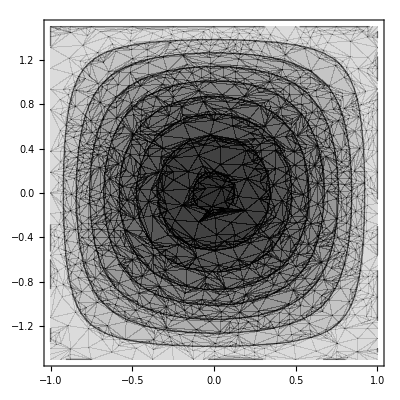
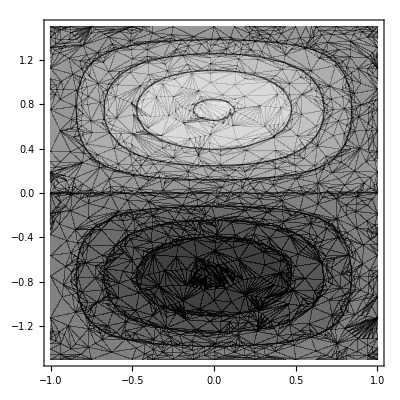
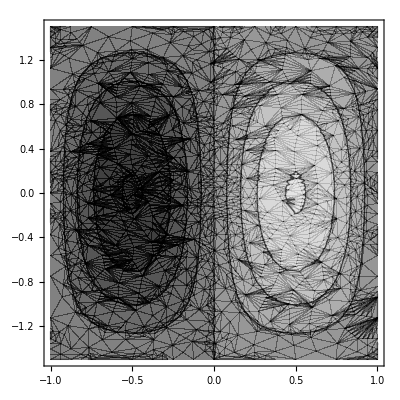
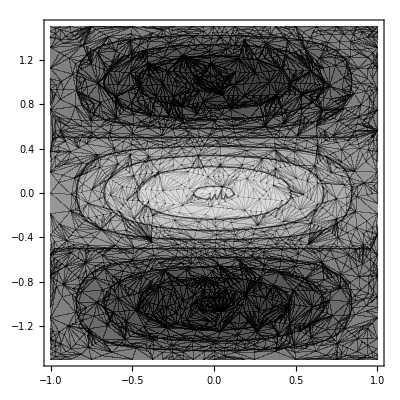
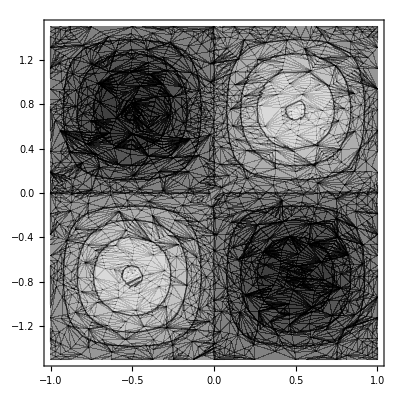
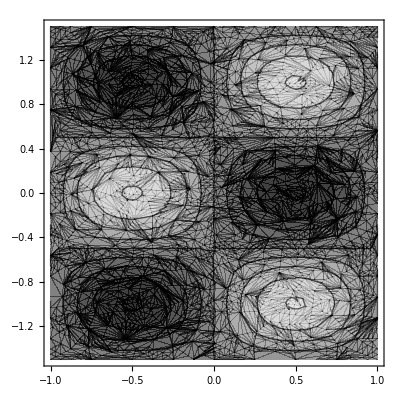
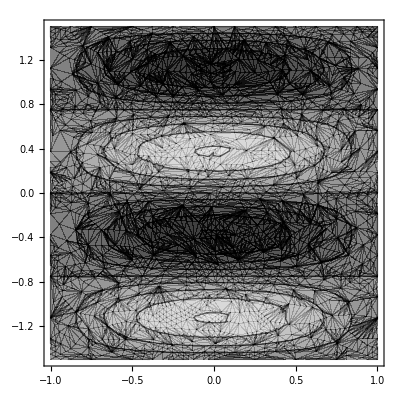
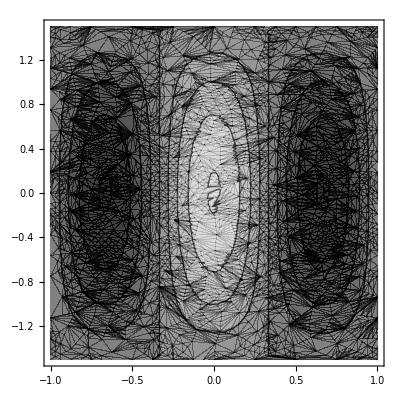

```mathematica
kontur = ContourPlot[#, {x,y} ∈ rectangle, PlotTheme→"Monochrome"] &/@ ReVectors
```

```mathematica
TableForm[{ReValues, kontur}]
```

3.56403 | 6.85392 | 10.9665 | 12.3373 | 14.2564 | 19.7397 | 20.0149 | 23.3061 | 26.596 | 27.4174 | 29.8888 | 32.0794 | 37.2913 | 39.7571 | 40.591 | 41.963
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-